# h=C+D+C^-1+D^-1

Computation of the sequences ρ := (|| h_n((||)_2)^2), ξ:=(ξ_n) , η:=(η_n),  ζ:=(ζ_n), m:=(m_n) , tables, graphs, and densities for the paper
“COMPUTATIONAL EXPLORATIONS OF THE THOMPSON GROUP T FOR THE AMENABILITY PROBLEM OF F” 
by S. Haagerup, U. Haagerup, M. Ramirez-Solano:

```mathematica
ρ={4,14,46,182,856,3888,20536,111366,642550,3850086,23444600,145705728,915645208,5816241006,37273096250,240608480566,1563526262404,10219209908952,67146704535028,443323828665766,2939893937656674,19575351631144042,130835022206113204,877529231836455728,5905019922806515884,39857811116595156626,269809546538449104054,1831388211478414017418}
```

{4,14,46,182,856,3888,20536,111366,642550,3850086,23444600,145705728,915645208,5816241006,37273096250,240608480566,1563526262404,10219209908952,67146704535028,443323828665766,2939893937656674,19575351631144042,130835022206113204,877529231836455728,5905019922806515884,39857811116595156626,269809546538449104054,1831388211478414017418}

```mathematica
q=4-1;
ξ=ρ-(q+1)Table[q^(n-1),{n,1,Length[ρ]}]
η=ξ-(q-1)Table[Total[ξ⟦Range[n-1]⟧],{n,1,Length[ξ]}]
ζ=η-(q-1)Table[Total[η⟦Range[n-1]⟧],{n,1,Length[ξ]}]
m=Table[Binomial[2n,n] q^n+Total[Table[Binomial[2n,n-k] q^(n-k)(ζ⟦k⟧+1-q),{k,1,n}]],{n,1,Length[ζ]}]
Ntuple=Length[m]
```

{0,2,10,74,532,2916,17620,102618,616306,3771354,23208404,144997140,913519444,5809863714,37253964374,240551084938,1563354075520,10218693348300,67145154853072,443319179619898,2939879990519070,19575309789731230,130834896681874768,877528855263740420,5905018793088369960,39857807727440718854,269809536370985790738,1831388180976024077470}

{0,2,6,50,360,1680,10552,60310,368762,2291198,14185540,89557468,568085492,3637390874,23461764106,152250955922,993951776628,6522582898368,43011657706540,284895372767222,1894817824426598,12650487642600618,84759454955281696,569783620173397812,3842215847470546512,25984967195646155486,176221080384309789662,1198180652247376494918}

{0,2,2,34,244,844,6356,35010,222842,1407754,8719700,55720548,355133636,2288268034,14837859518,96703523122,633902431984,4174630000468,27618539011904,183478938659506,1223610644784438,8189644814105262,54997636841585104,370502892149137828,2503367879099490904,16961687532334006854,115227866329705330058,784745277424152455990}

{4,30,270,2678,28418,317246,3681822,44027350,538815546,6714321830,84869473770,1085055369622,14001672259722,182071429751606,2382930531465042,31360608130235654,414711515674495370,5507403086681142854,73415226964469375622,981973882890399349286,13175045740884220099018,177267112861509055927594,2391279755795301975623294,32335124616320091148224950,438214977894105234044150738,5951190674684154918623110822,80978038411680591548914827558,1103891232023903090341589166522}

28

```mathematica
mq=Table[Binomial[2n,n] q^n+Total[Table[Binomial[2n,n-k] q^(n-k)(1-q),{k,1,n}]],{n,1,Length[m]}]
```

{4,28,232,2092,19864,195352,1970896,20275660,211823800,2240795848,23951289520,258255469816,2805534253552,30675477376432,337306474674592,3727578443380492,41376874025687032,461121792658583272,5157384457905440752,57869888433073055272,651266142688270063312,7349148747954997832272,83136542574028253115232,942624010510370287581112,10710299802962282322975664,121931135179324562174275792,1390649997297710838197284576,15887581504915826061300169840}

```mathematica
(*Clear[ζ,ξ]
ζ[1]=m⟦1⟧-mq⟦1⟧;
Table[ζ[n]=m⟦n⟧-mq⟦n⟧-Total[Table[Binomial[2n,k] q^k ζ[n-k],{k,1,n-1}]],{n,2,Length[m]}];
Clear[η]
η[1]=ζ[1];
Table[η[n]=ζ[n]+(q-1)Total[Table[q^(i-1) ζ[n-i],{i,1,n-1}]],{n,2,Ntuple}];
ξ[1]=η[1];
Table[ξ[n]=η[n]+(q-1)Total[Table[q^(i-1) η[n-i],{i,1,n-1}]],{n,2,Ntuple}];
ξ=Table[ξ[n],{n,1,Length[m]}]
η=Table[η[n],{n,1,Length[m]}]
ζ=Table[ζ[n],{n,1,Length[m]}]
hnList=ξ+(q+1)Table[q^(n-1),{n,1,Length[m]}]*)
```

{0,2,10,74,532,2916,17620,102618,616306,3771354,23208404,144997140,913519444,5809863714,37253964374,240551084938,1563354075520,10218693348300,67145154853072,443319179619898,2939879990519070,19575309789731230,130834896681874768,877528855263740420}

{0,2,6,50,360,1680,10552,60310,368762,2291198,14185540,89557468,568085492,3637390874,23461764106,152250955922,993951776628,6522582898368,43011657706540,284895372767222,1894817824426598,12650487642600618,84759454955281696,569783620173397812}

{0,2,2,34,244,844,6356,35010,222842,1407754,8719700,55720548,355133636,2288268034,14837859518,96703523122,633902431984,4174630000468,27618539011904,183478938659506,1223610644784438,8189644814105262,54997636841585104,370502892149137828}

{4,14,46,182,856,3888,20536,111366,642550,3850086,23444600,145705728,915645208,5816241006,37273096250,240608480566,1563526262404,10219209908952,67146704535028,443323828665766,2939893937656674,19575351631144042,130835022206113204,877529231836455728}

```mathematica
(*Clear[ζ]
ζ[1]=m[[1]]-mq[[1]]
Table[ζ[n]=m⟦n⟧-mq⟦n⟧-Total[Table[Binomial[2n,k] q^k ζ[n-k],{k,1,n-1}]],{n,2,Length[m]}]
ζ=Table[ζ[n],{n,1,Length[m]}]*)
```

0

{2,2,34,244,844,6356,35010,222842,1407754,8719700,55720548,355133636,2288268034,14837859518,96703523122,633902431984,4174630000468,27618539011904,183478938659506,1223610644784438,8189644814105262,54997636841585104,370502892149137828}

{0,2,2,34,244,844,6356,35010,222842,1407754,8719700,55720548,355133636,2288268034,14837859518,96703523122,633902431984,4174630000468,27618539011904,183478938659506,1223610644784438,8189644814105262,54997636841585104,370502892149137828}

```mathematica
Grid[Transpose[{Range[Length[m]],ρ,η,ζ,m}],Alignment->Left]
```

1 | 4 | 0 | 0 | 4
2 | 14 | 2 | 2 | 30
3 | 46 | 6 | 2 | 270
4 | 182 | 50 | 34 | 2678
5 | 856 | 360 | 244 | 28418
6 | 3888 | 1680 | 844 | 317246
7 | 20536 | 10552 | 6356 | 3681822
8 | 111366 | 60310 | 35010 | 44027350
9 | 642550 | 368762 | 222842 | 538815546
10 | 3850086 | 2291198 | 1407754 | 6714321830
11 | 23444600 | 14185540 | 8719700 | 84869473770
12 | 145705728 | 89557468 | 55720548 | 1085055369622
13 | 915645208 | 568085492 | 355133636 | 14001672259722
14 | 5816241006 | 3637390874 | 2288268034 | 182071429751606
15 | 37273096250 | 23461764106 | 14837859518 | 2382930531465042
16 | 240608480566 | 152250955922 | 96703523122 | 31360608130235654
17 | 1563526262404 | 993951776628 | 633902431984 | 414711515674495370
18 | 10219209908952 | 6522582898368 | 4174630000468 | 5507403086681142854
19 | 67146704535028 | 43011657706540 | 27618539011904 | 73415226964469375622
20 | 443323828665766 | 284895372767222 | 183478938659506 | 981973882890399349286
21 | 2939893937656674 | 1894817824426598 | 1223610644784438 | 13175045740884220099018
22 | 19575351631144042 | 12650487642600618 | 8189644814105262 | 177267112861509055927594
23 | 130835022206113204 | 84759454955281696 | 54997636841585104 | 2391279755795301975623294
24 | 877529231836455728 | 569783620173397812 | 370502892149137828 | 32335124616320091148224950
25 | 5905019922806515884 | 3842215847470546512 | 2503367879099490904 | 438214977894105234044150738
26 | 39857811116595156626 | 25984967195646155486 | 16961687532334006854 | 5951190674684154918623110822
27 | 269809546538449104054 | 176221080384309789662 | 115227866329705330058 | 80978038411680591548914827558
28 | 1831388211478414017418 | 1198180652247376494918 | 784745277424152455990 | 1103891232023903090341589166522

```mathematica
Clear[d]
```

```mathematica
mm=Riffle[0Range[Length[m]],m]
Table[d[n]=Det[Table[If[i+j==0,1,mm⟦i+j⟧],{i,0,n},{j,0,n}]],{n,0,Length[m]}]
d[-1]=1;
Table[k[n]=(d[n-1]/d[n])^(1/2),{n,0,Length[m]}];
Table[α[n]=k[n-1]/k[n],{n,1,Length[m]}];
```

{0,4,0,30,0,270,0,2678,0,28418,0,317246,0,3681822,0,44027350,0,538815546,0,6714321830,0,84869473770,0,1085055369622,0,14001672259722,0,182071429751606,0,2382930531465042,0,31360608130235654,0,414711515674495370,0,5507403086681142854,0,73415226964469375622,0,981973882890399349286,0,13175045740884220099018,0,177267112861509055927594,0,2391279755795301975623294,0,32335124616320091148224950,0,438214977894105234044150738,0,5951190674684154918623110822,0,80978038411680591548914827558,0,1103891232023903090341589166522}

{1,4,56,2520,430560,308816768,661165339136,5459669516838912,143776955507210625024,14323178370690420646477824,5697201929482010493644993200128,6958841326618649982297123879674445824,34771885236812667146352840283958530264793088,557806010726414741470538508951509752132371801440256,34125304244431518252734968943396995796752850530910045470720,8196413659005781017466688205193296565345344625281052437297569464320,6045525736277037953557191035131127945644800425139117225533133636339838746624,18395529637842888997082805705705346893023250024888668520037496709357617264000466157568,184675695901097259255312775027486900239175676168267041152130411205366120532210000372406471884800,7220905493920633159602647901874499602162013822428872224623846258495163669295535523759264135876074222387200,1060274147619901881438564260925049951462050385320433029752765276958005603237981248777217181976011133115439071738462208,497421867242670225522035313012393998823939420656797087269165798741100108770443238793184502728455960540016255926647595883246387200,953601889378776658301238909220992455734508550662773858012670852660579123222936839447902667935643255645500414999842772038815053025832547123200,6087396974714399780317086433604789041342621896330041039111735685400966061077202775757462510816452400851948659854220410377299422058092077015831502779318272,155616684294481621362545823247062232484708237860345825292253953462322109075659708218534817417259078364649269251526514873528670258770494824937694158490359186777448644608,14159302133044852240675856016655328751145169333278182255838416865801871169130618462781502611371301429044506415737385242131970476099502035363710178748646656993017401204274062744879104,4357717995298820430225643474936776309236916000356079447137456841558526757524853636210347537366994251413666174249861767834474022950463852978756744588506328602489795904367301569739744807050977214464,5398813602054744194087814472402341676424499134048364043614879184705262304357208726016734933561887490490530774660598044941921933006645730396991354997266351479955388555297017349383324190049426469890704658179031040,22319475623542837115451706101055508514530115220046010987019270378349077849987291745712405902818368756432460242063731195448545338976554467815439262939565643290152068506382842874012561045508841100272183186324866663778782480957440}

```mathematica
(*Table[α[n],{n,1,Ntuple}]//N*)
```

{2.,1.87083,1.79284,1.94854,2.04888,1.72771,1.96392,1.7858,1.94497,1.99819,1.75237,2.02259,1.79177,1.95285,1.98142,1.75239,2.03111,1.81639,1.97352,1.93786,1.78748,2.02147,1.82478,2.00115}

```mathematica
(*Table[((d[n-2] d[n])/d[n-1]^2)^(1/2),{n,1,Ntuple}]//N*)
```

{2.,1.87083,1.79284,1.94854,2.04888,1.72771,1.96392,1.7858,1.94497,1.99819,1.75237,2.02259,1.79177,1.95285,1.98142,1.75239,2.03111,1.81639,1.97352,1.93786,1.78748,2.02147,1.82478,2.00115}

```mathematica
(*Next we use a trick. It agrees with the one with non trick and using the reals*)
```

```mathematica
MnormFunctiontest=Function[n,Module[{i,j,eigenvalues,A},
A=Table[0,{i,1,n+1},{j,1,n+1}];
Table[A⟦i,i+1⟧=α[i]^2,{i,1,n}];
Table[A⟦i+1,i⟧=1,{i,1,n}];
A
]];
Table[(MnormFunctiontest[i]//MatrixForm),{i,0,7}]
MnormFunction=Function[n,Module[{i,j,eigenvalues,A},
A=Table[0,{i,1,n+1},{j,1,n+1}];
Table[A⟦i,i+1⟧=α[i]^2,{i,1,n}];
Table[A⟦i+1,i⟧=1,{i,1,n}];
eigenvalues=Eigenvalues[A];
eigenvalues=eigenvalues//N;
Max[eigenvalues]
]];
Table[Mnorm[i]=MnormFunction[i],{i,0,Length[m]}]
```

{(0),(0 | 4
1 | 0),(0 | 4 | 0
1 | 0 | 7/2
0 | 1 | 0),(0 | 4 | 0 | 0
1 | 0 | 7/2 | 0
0 | 1 | 0 | 45/14
0 | 0 | 1 | 0),(0 | 4 | 0 | 0 | 0
1 | 0 | 7/2 | 0 | 0
0 | 1 | 0 | 45/14 | 0
0 | 0 | 1 | 0 | 1196/315
0 | 0 | 0 | 1 | 0),(0 | 4 | 0 | 0 | 0 | 0
1 | 0 | 7/2 | 0 | 0 | 0
0 | 1 | 0 | 45/14 | 0 | 0
0 | 0 | 1 | 0 | 1196/315 | 0
0 | 0 | 0 | 1 | 0 | 56483/13455
0 | 0 | 0 | 0 | 1 | 0),(0 | 4 | 0 | 0 | 0 | 0 | 0
1 | 0 | 7/2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 45/14 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1196/315 | 0 | 0
0 | 0 | 0 | 1 | 0 | 56483/13455 | 0
0 | 0 | 0 | 0 | 1 | 0 | 7201665/2412631
0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 4 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 7/2 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 45/14 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1196/315 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 56483/13455 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 7201665/2412631 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 262140177/67965187
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

{0.,2.,2.73861,3.0557,3.25861,3.42926,3.51875,3.57859,3.61369,3.63956,3.66407,3.68118,3.69704,3.70881,3.71884,3.72895,3.73636,3.74354,3.74935,3.75482,3.7603,3.76455,3.76876,3.77227,3.77583,3.77924,3.78205,3.7849,3.7873}

{2.,1.87083,1.79284,1.94854,2.04888,1.72771,1.96392,1.7858,1.94497,1.99819,1.75237,2.02259,1.79177,1.95285,1.98142,1.75239,2.03111,1.81639,1.97352,1.93786,1.78748,2.02147,1.82478,2.00115,1.8866,1.83914,2.00637,1.82673}

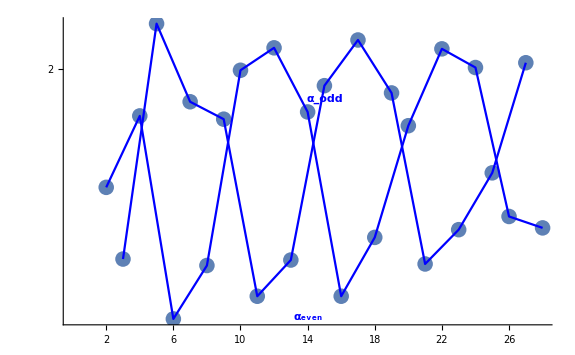

```mathematica
Table[α[n],{n,1,Ntuple}]//N
Show[
ListPlot[Table[{i,α[i]},{i,2,Ntuple}],Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}],
ListPlot[Table[{i,α[i]},{i,2,Ntuple,2}],Joined->True,PlotStyle->{Blue}],ListPlot[Table[{i,α[i]},{i,3,Ntuple,2}],Joined->True,PlotStyle->{Blue}],
Graphics[{Blue,Text[Style[HoldForm[Subscript[α, even]],Large,Bold],{14,.002+α[6]}]}],
Graphics[{Blue,Text[Style[HoldForm[Subscript[α, odd]],Large,Bold],{15,.003+α[7]}]}]
]
```

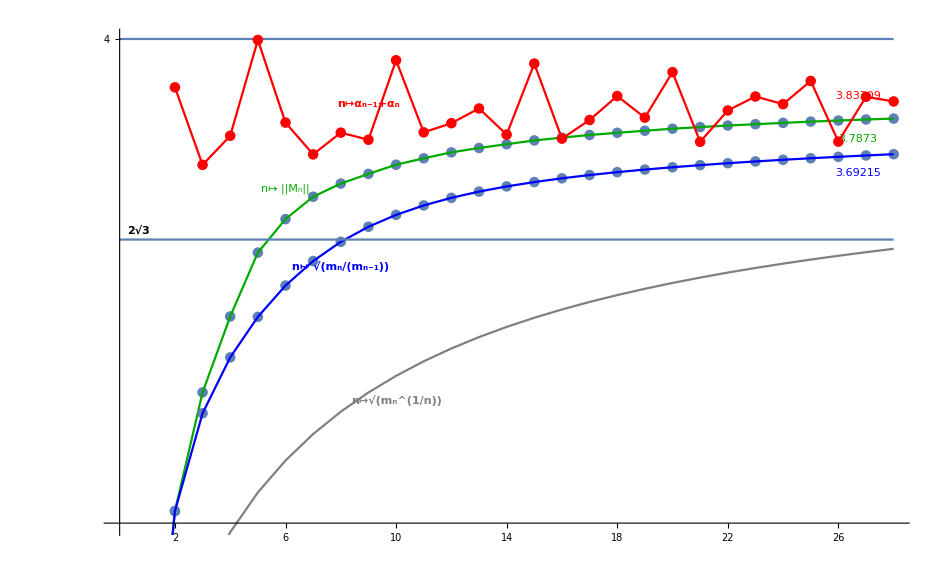

```mathematica
ma[0]=1;
Table[ma[i]=m⟦i⟧,{i,1,Length[m]}];
A=Show[
ListPlot[Table[{i,Mnorm[i]},{i,0,Ntuple}],Ticks->{Range[2,Ntuple,2]},PlotStyle->{PointSize[.008]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotRange->{2.7,4}],
ListPlot[Table[{i,Mnorm[i]},{i,0,Ntuple}],Joined->True,PlotStyle->{Darker[Green]}],
Graphics[{Darker[Green],Text[Style[HoldForm["n↦ ||M_n||"],Large],{6,.08+Mnorm[6]}]}],
Graphics[{Darker[Green],Text[Style[Mnorm[Ntuple],Large],{Ntuple-1.3,-.055+Mnorm[Ntuple]}]}],
Graphics[{Red,Text[Style[N[α[Ntuple-1]+α[Ntuple]],Large],{Ntuple-1.3,.015+α[Ntuple-1]+α[Ntuple]}]}],
Graphics[{Blue,Text[Style[N[(ma[Ntuple]/ma[Ntuple-1])^(1/2)],Large],{Ntuple-1.3,-.05+(ma[Ntuple]/ma[Ntuple-1])^(1/2)}]}],
Plot[8,{x,0,Ntuple}],
ListPlot[Table[{i,(ma[i]/ma[i-1])^(1/2)},{i,1,Ntuple}],Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotStyle->{PointSize[.008]}],
ListPlot[Table[{i,(ma[i]/ma[i-1])^(1/2)},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Blue,PointSize[.008]}],
Graphics[{Blue,Text[Style[HoldForm[n↦(Subscript[m, n]/Subscript[m, n-1])^(1/2)],Large,Bold],{8,-.065+(ma[8]/ma[7])^(1/2)}]}],
ListPlot[Table[{i,α[i-1]+α[i]},{i,1,Ntuple}],PlotStyle->{Red,PointSize[.008]},Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}],
ListPlot[Table[{i,α[i-1]+α[i]},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Red}],
Graphics[{Red,Text[Style[HoldForm[n↦Subscript[α, n-1]+Subscript[α, n]],Large,Bold],{10-1,.05+α[5]+α[6]}]}],
ListPlot[Table[{i,(ma[i]^(1/i))^(1/2)},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Gray}],
Graphics[{Gray,Text[Style[HoldForm[n↦√((Subscript[m, n])^(1/n))],Large,Bold],{10,-.065+(ma[10]^(1/10))^(1/2)}]}],
Graphics[{Black,Text[Style[HoldForm["2√3"],Medium,Bold],{.7,2 Sqrt[3]+.025}]}],
Plot[Sqrt[12],{x,0,Ntuple}],
Plot[4,{x,0,Ntuple}]

]
```

```mathematica
Grid[Transpose[
{Range[Length[m]],
N[Table[(ma[i]^(1/i))^(1/2),{i,1,Ntuple,1}],6],
N[Table[(ma[i]/ma[i-1])^(1/2),{i,1,Ntuple}],6],
N[Table[α[n],{n,1,Ntuple}],6],
N[Table[Mnorm[i],{i,1,Ntuple}],6],
N[Table[α[i-1]+α[i],{i,1,Ntuple}],6]}
],Alignment->Left]
```

1 | 2. | 2. | 2. | 2. | 2.+α[0]
2 | 2.34035 | 2.73861 | 1.87083 | 2.73861 | 3.87083
3 | 2.5423 | 3. | 1.79284 | 3.0557 | 3.66367
4 | 2.68211 | 3.14937 | 1.94854 | 3.25861 | 3.74139
5 | 2.78843 | 3.25755 | 2.04888 | 3.42926 | 3.99743
6 | 2.87375 | 3.34119 | 1.72771 | 3.51875 | 3.77659
7 | 2.94445 | 3.4067 | 1.96392 | 3.57859 | 3.69163
8 | 3.00423 | 3.45804 | 1.7858 | 3.61369 | 3.74972
9 | 3.05548 | 3.49831 | 1.94497 | 3.63956 | 3.73078
10 | 3.09992 | 3.53005 | 1.99819 | 3.66407 | 3.94316
11 | 3.13878 | 3.55529 | 1.75237 | 3.68118 | 3.75056
12 | 3.17305 | 3.57561 | 2.02259 | 3.69704 | 3.77496
13 | 3.20348 | 3.59223 | 1.79177 | 3.70881 | 3.81436
14 | 3.23068 | 3.60604 | 1.95285 | 3.71884 | 3.74462
15 | 3.25515 | 3.61772 | 1.98142 | 3.72895 | 3.93427
16 | 3.27727 | 3.62774 | 1.75239 | 3.73636 | 3.73381
17 | 3.29738 | 3.63648 | 2.03111 | 3.74354 | 3.78351
18 | 3.31575 | 3.64418 | 1.81639 | 3.74935 | 3.8475
19 | 3.33261 | 3.65107 | 1.97352 | 3.75482 | 3.78992
20 | 3.34813 | 3.65727 | 1.93786 | 3.7603 | 3.91138
21 | 3.36249 | 3.66291 | 1.78748 | 3.76455 | 3.72534
22 | 3.37581 | 3.66807 | 2.02147 | 3.76876 | 3.80895
23 | 3.38821 | 3.67283 | 1.82478 | 3.77227 | 3.84625
24 | 3.39979 | 3.67724 | 2.00115 | 3.77583 | 3.82593
25 | 3.41062 | 3.68134 | 1.8866 | 3.77924 | 3.88775
26 | 3.42079 | 3.68518 | 1.83914 | 3.78205 | 3.72575
27 | 3.43036 | 3.68877 | 2.00637 | 3.7849 | 3.84551
28 | 3.43939 | 3.69215 | 1.82673 | 3.7873 | 3.83309

```mathematica
Tcase={0.,2.,2.7386127875258306,3.055703412859072,3.2586121569734106,3.4292609360165467,3.5187496979405797,3.5785926127769545,3.6136924357999027,3.639563973564201,3.6640652912973164,3.6811799245405408,3.6970415388301285,3.7088089364021144,3.718835559697048,3.7289515865989724,3.736356750583295,3.743544352777439,3.7493533842351234,3.7548227934145477,3.760297930689068,3.764546154871844,3.768760183628806,3.7722698721396735,3.775826287530374}
```

{0.,2.,2.73861,3.0557,3.25861,3.42926,3.51875,3.57859,3.61369,3.63956,3.66407}

{0.,2.,2.73861,3.0557,3.25861,3.42926,3.51875,3.57859,3.61369,3.63956,3.66407,3.68118,3.69704,3.70881,3.71884,3.72895,3.73636,3.74354,3.74935}

{0.,2.,2.73861,3.0557,3.25861,3.42926,3.51875,3.57859,3.61369,3.63956,3.66407,3.68118,3.69704,3.70881,3.71884,3.72895,3.73636,3.74354,3.74935,3.75482}

{0.,2.,2.73861,3.0557,3.25861,3.42926,3.51875,3.57859,3.61369,3.63956,3.66407,3.68118,3.69704,3.70881,3.71884,3.72895,3.73636,3.74354,3.74935,3.75482,3.7603}

{0.,2.,2.73861,3.0557,3.25861,3.42926,3.51875,3.57859,3.61369,3.63956,3.66407,3.68118,3.69704,3.70881,3.71884,3.72895,3.73636,3.74354,3.74935,3.75482,3.7603,3.76455,3.76876}

{0.,2.,2.73861,3.0557,3.25861,3.42926,3.51875,3.57859,3.61369,3.63956,3.66407,3.68118,3.69704,3.70881,3.71884,3.72895,3.73636,3.74354,3.74935,3.75482,3.7603,3.76455,3.76876,3.77227}

{0.,2.,2.73861,3.0557,3.25861,3.42926,3.51875,3.57859,3.61369,3.63956,3.66407,3.68118,3.69704,3.70881,3.71884,3.72895,3.73636,3.74354,3.74935,3.75482,3.7603,3.76455,3.76876,3.77227,3.77583}

```mathematica
Fcase={0.,2.,2.6457513110645907,2.9335219916448536,3.0889126347550055,3.1918358385144856,3.2643903643756125,3.319998303127948,3.3627564463846538,3.3978988679096824,3.426818714263687,3.451637737813765,3.4727238535489615,3.491329371785696,3.5075519932429198,3.522166264757021,3.535130300450429,3.5469663302982184,3.557611852032139,3.567447136111488,3.576385735755989,3.584713309199795,3.592350504371768,3.599515792187644,3.6061319156020772,3.6123787238443597,3.618181132463141,3.6236865144922032,3.62882651417,3.633724335678147,3.6383166967516467,3.6427101578103804}
```

{0.,2.,2.64575,2.93352,3.08891,3.19184,3.26439,3.32,3.36276,3.3979,3.42682,3.45164,3.47272,3.49133,3.50755,3.52217,3.53513,3.54697,3.55761,3.56745,3.57639,3.58471,3.59235,3.59952,3.60613,3.61238,3.61818,3.62369,3.62883,3.63372,3.63832,3.64271}

```mathematica
3.8206792144809496-2.4977361725011833/(-0.48+x-1)^1.2329498569632982
3.8289897950143055-2.3665883343423277/(-0.48+x-1)^1.1847829719307073
3.8412444735377003-2.257633327972807/(-0.48+x)^1.124053882386779
```

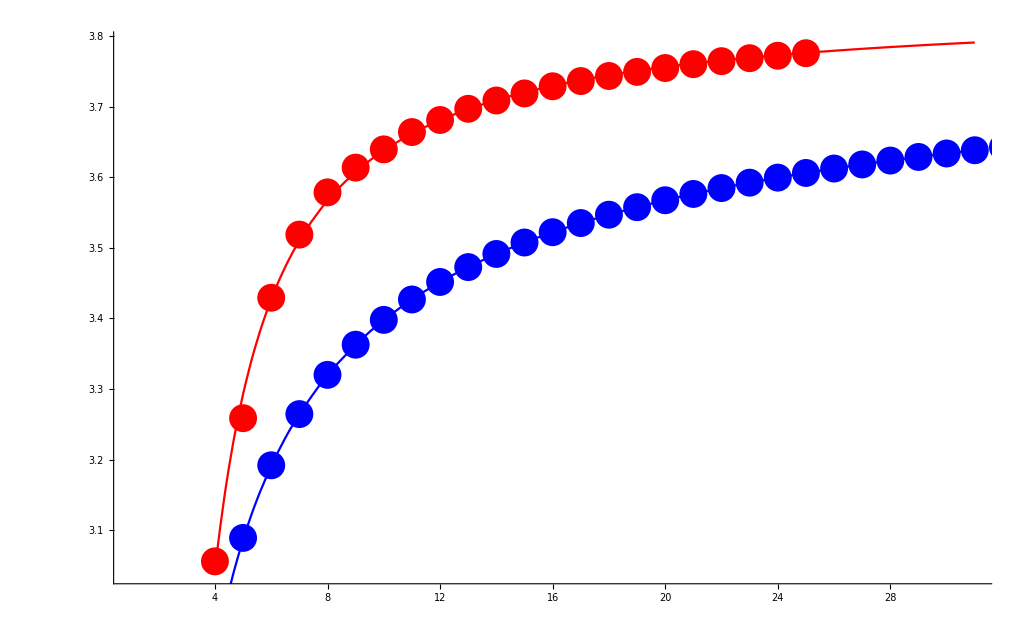

```mathematica
Show[Plot[3.8412444735377003-2.257633327972807/(-0.48+x-1)^1.124053882386779,{x,1,31},PlotStyle->Red],ListPlot[Tcase,PlotStyle->Red],ListPlot[Fcase, PlotStyle->Blue],Plot[3.8700685881870855-1.612013242983189/(-0.48+x-1)^0.5730517987465562,{x,1,31},PlotStyle->Blue]]
```

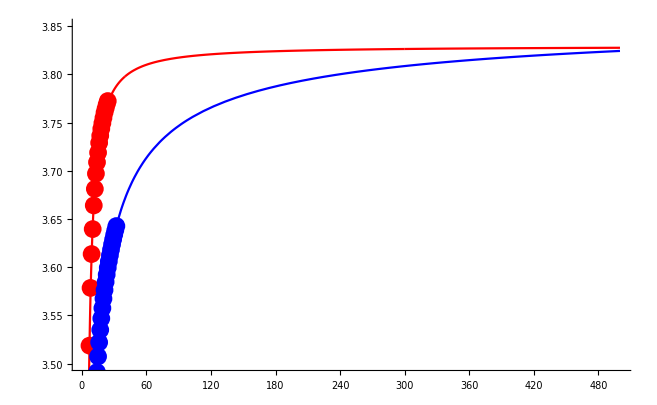

```mathematica
Show[Plot[3.8289897950143055-2.3665883343423277/(-0.48+x-1)^1.1847829719307073,{x,1,40},PlotStyle->Red],Plot[3.8289897950143055-2.3665883343423277/(-0.48+x-1)^1.1847829719307073,{x,40,300},PlotStyle->Red],Plot[3.8289897950143055-2.3665883343423277/(-0.48+x-1)^1.1847829719307073,{x,300,500},PlotStyle->Red],ListPlot[Tcase,PlotStyle->Red],ListPlot[Fcase, PlotStyle->Blue],Plot[3.8700685881870855-1.612013242983189/(-0.48+x-1)^0.5730517987465562,{x,1,500},PlotStyle->Blue],PlotRange->{{1,500},{3.5,3.85}}]
```